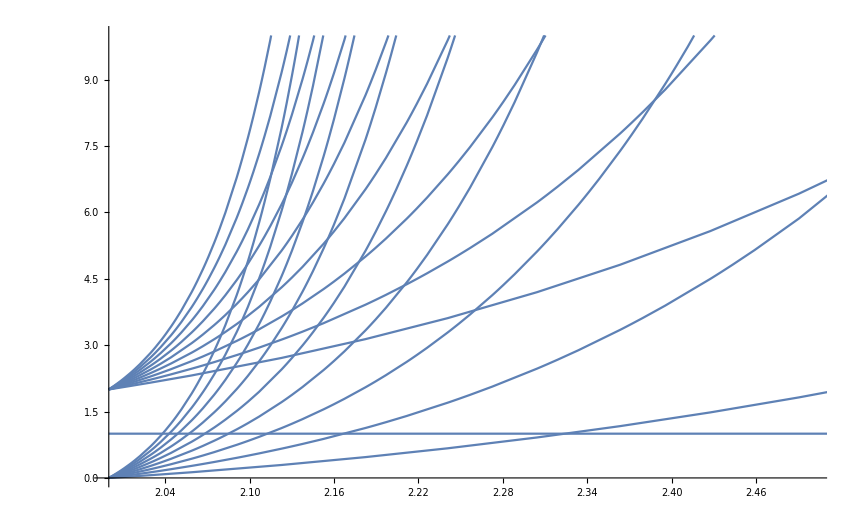

{1,-2+x,-1+x,x,3-3 x+x^2,2-2 x+x^2,5-10 x+10 x^2-5 x^3+x^4,1-x+x^2,7-21 x+35 x^2-35 x^3+21 x^4-7 x^5+x^6,2-4 x+6 x^2-4 x^3+x^4,3-9 x+18 x^2-21 x^3+15 x^4-6 x^5+x^6,1-2 x+4 x^2-3 x^3+x^4,11-55 x+165 x^2-330 x^3+462 x^4-462 x^5+330 x^6-165 x^7+55 x^8-11 x^9+x^10,1-2 x+5 x^2-4 x^3+x^4,13-78 x+286 x^2-715 x^3+1287 x^4-1716 x^5+1716 x^6-1287 x^7+715 x^8-286 x^9+78 x^10-13 x^11+x^12,1-3 x+9 x^2-13 x^3+11 x^4-5 x^5+x^6,1-4 x+14 x^2-28 x^3+39 x^4-36 x^5+21 x^6-7 x^7+x^8,2-8 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,17-136 x+680 x^2-2380 x^3+6188 x^4-12376 x^5+19448 x^6-24310 x^7+24310 x^8-19448 x^9+12376 x^10-6188 x^11+2380 x^12-680 x^13+136 x^14-17 x^15+x^16,1-3 x+12 x^2-19 x^3+15 x^4-6 x^5+x^6,19-171 x+969 x^2-3876 x^3+11628 x^4-27132 x^5+50388 x^6-75582 x^7+92378 x^8-92378 x^9+75582 x^10-50388 x^11+27132 x^12-11628 x^13+3876 x^14-969 x^15+171 x^16-19 x^17+x^18}

```mathematica
Plot[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,20}]]],{x,2,5}, PlotRange->{{2,2.5},{0,10}}]
```

```mathematica
{1,-2+x,-1+x,x,3-3 x+x^2,2-2 x+x^2,5-10 x+10 x^2-5 x^3+x^4,1-x+x^2,7-21 x+35 x^2-35 x^3+21 x^4-7 x^5+x^6,2-4 x+6 x^2-4 x^3+x^4,3-9 x+18 x^2-21 x^3+15 x^4-6 x^5+x^6,1-2 x+4 x^2-3 x^3+x^4,11-55 x+165 x^2-330 x^3+462 x^4-462 x^5+330 x^6-165 x^7+55 x^8-11 x^9+x^10,1-2 x+5 x^2-4 x^3+x^4,13-78 x+286 x^2-715 x^3+1287 x^4-1716 x^5+1716 x^6-1287 x^7+715 x^8-286 x^9+78 x^10-13 x^11+x^12,1-3 x+9 x^2-13 x^3+11 x^4-5 x^5+x^6,1-4 x+14 x^2-28 x^3+39 x^4-36 x^5+21 x^6-7 x^7+x^8,2-8 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,17-136 x+680 x^2-2380 x^3+6188 x^4-12376 x^5+19448 x^6-24310 x^7+24310 x^8-19448 x^9+12376 x^10-6188 x^11+2380 x^12-680 x^13+136 x^14-17 x^15+x^16,1-3 x+12 x^2-19 x^3+15 x^4-6 x^5+x^6,19-171 x+969 x^2-3876 x^3+11628 x^4-27132 x^5+50388 x^6-75582 x^7+92378 x^8-92378 x^9+75582 x^10-50388 x^11+27132 x^12-11628 x^13+3876 x^14-969 x^15+171 x^16-19 x^17+x^18}//Length
```

21

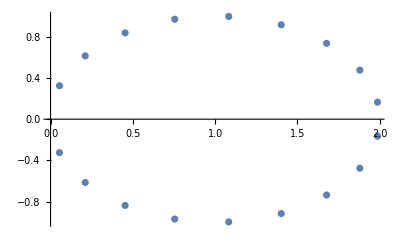

```mathematica
Map[{Re[#[[2]]],Im[#[[2]]]}&,ExpressionToList[N[Roots[19-171 x+969 x^2-3876 x^3+11628 x^4-27132 x^5+50388 x^6-75582 x^7+92378 x^8-92378 x^9+75582 x^10-50388 x^11+27132 x^12-11628 x^13+3876 x^14-969 x^15+171 x^16-19 x^17+x^18==0,x]]]]//ListPlot
```

```mathematica
Roots[Function[x,2 x-3 x^2+x^3]==0,x]
```

False

```mathematica
Table[ExpressionToList[k],{k,{Function[x,2 x-3 x^2+x^3],Function[x,-3 x+6 x^2-4 x^3+x^4],Function[x,4 x-10 x^2+10 x^3-5 x^4+x^5],Function[x,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6],Function[x,6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7],Function[x,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8],Function[x,8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9],Function[x,-9 x+45 x^2-120 x^3+210 x^4-252 x^5+210 x^6-120 x^7+45 x^8-10 x^9+x^10],Function[x,10 x-55 x^2+165 x^3-330 x^4+462 x^5-462 x^6+330 x^7-165 x^8+55 x^9-11 x^10+x^11],Function[x,-11 x+66 x^2-220 x^3+495 x^4-792 x^5+924 x^6-792 x^7+495 x^8-220 x^9+66 x^10-12 x^11+x^12],Function[x,12 x-78 x^2+286 x^3-715 x^4+1287 x^5-1716 x^6+1716 x^7-1287 x^8+715 x^9-286 x^10+78 x^11-13 x^12+x^13],Function[x,-13 x+91 x^2-364 x^3+1001 x^4-2002 x^5+3003 x^6-3432 x^7+3003 x^8-2002 x^9+1001 x^10-364 x^11+91 x^12-14 x^13+x^14],Function[x,14 x-105 x^2+455 x^3-1365 x^4+3003 x^5-5005 x^6+6435 x^7-6435 x^8+5005 x^9-3003 x^10+1365 x^11-455 x^12+105 x^13-15 x^14+x^15],Function[x,-15 x+120 x^2-560 x^3+1820 x^4-4368 x^5+8008 x^6-11440 x^7+12870 x^8-11440 x^9+8008 x^10-4368 x^11+1820 x^12-560 x^13+120 x^14-16 x^15+x^16],Function[x,16 x-136 x^2+680 x^3-2380 x^4+6188 x^5-12376 x^6+19448 x^7-24310 x^8+24310 x^9-19448 x^10+12376 x^11-6188 x^12+2380 x^13-680 x^14+136 x^15-17 x^16+x^17],Function[x,-17 x+153 x^2-816 x^3+3060 x^4-8568 x^5+18564 x^6-31824 x^7+43758 x^8-48620 x^9+43758 x^10-31824 x^11+18564 x^12-8568 x^13+3060 x^14-816 x^15+153 x^16-18 x^17+x^18],Function[x,18 x-171 x^2+969 x^3-3876 x^4+11628 x^5-27132 x^6+50388 x^7-75582 x^8+92378 x^9-92378 x^10+75582 x^11-50388 x^12+27132 x^13-11628 x^14+3876 x^15-969 x^16+171 x^17-19 x^18+x^19],Function[x,-19 x+190 x^2-1140 x^3+4845 x^4-15504 x^5+38760 x^6-77520 x^7+125970 x^8-167960 x^9+184756 x^10-167960 x^11+125970 x^12-77520 x^13+38760 x^14-15504 x^15+4845 x^16-1140 x^17+190 x^18-20 x^19+x^20]}}]
```

{{x,2 x-3 x^2+x^3},{x,-3 x+6 x^2-4 x^3+x^4},{x,4 x-10 x^2+10 x^3-5 x^4+x^5},{x,-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6},{x,6 x-21 x^2+35 x^3-35 x^4+21 x^5-7 x^6+x^7},{x,-7 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8},{x,8 x-36 x^2+84 x^3-126 x^4+126 x^5-84 x^6+36 x^7-9 x^8+x^9},{x,-9 x+45 x^2-120 x^3+210 x^4-252 x^5+210 x^6-120 x^7+45 x^8-10 x^9+x^10},{x,10 x-55 x^2+165 x^3-330 x^4+462 x^5-462 x^6+330 x^7-165 x^8+55 x^9-11 x^10+x^11},{x,-11 x+66 x^2-220 x^3+495 x^4-792 x^5+924 x^6-792 x^7+495 x^8-220 x^9+66 x^10-12 x^11+x^12},{x,12 x-78 x^2+286 x^3-715 x^4+1287 x^5-1716 x^6+1716 x^7-1287 x^8+715 x^9-286 x^10+78 x^11-13 x^12+x^13},{x,-13 x+91 x^2-364 x^3+1001 x^4-2002 x^5+3003 x^6-3432 x^7+3003 x^8-2002 x^9+1001 x^10-364 x^11+91 x^12-14 x^13+x^14},{x,14 x-105 x^2+455 x^3-1365 x^4+3003 x^5-5005 x^6+6435 x^7-6435 x^8+5005 x^9-3003 x^10+1365 x^11-455 x^12+105 x^13-15 x^14+x^15},{x,-15 x+120 x^2-560 x^3+1820 x^4-4368 x^5+8008 x^6-11440 x^7+12870 x^8-11440 x^9+8008 x^10-4368 x^11+1820 x^12-560 x^13+120 x^14-16 x^15+x^16},{x,16 x-136 x^2+680 x^3-2380 x^4+6188 x^5-12376 x^6+19448 x^7-24310 x^8+24310 x^9-19448 x^10+12376 x^11-6188 x^12+2380 x^13-680 x^14+136 x^15-17 x^16+x^17},{x,-17 x+153 x^2-816 x^3+3060 x^4-8568 x^5+18564 x^6-31824 x^7+43758 x^8-48620 x^9+43758 x^10-31824 x^11+18564 x^12-8568 x^13+3060 x^14-816 x^15+153 x^16-18 x^17+x^18},{x,18 x-171 x^2+969 x^3-3876 x^4+11628 x^5-27132 x^6+50388 x^7-75582 x^8+92378 x^9-92378 x^10+75582 x^11-50388 x^12+27132 x^13-11628 x^14+3876 x^15-969 x^16+171 x^17-19 x^18+x^19},{x,-19 x+190 x^2-1140 x^3+4845 x^4-15504 x^5+38760 x^6-77520 x^7+125970 x^8-167960 x^9+184756 x^10-167960 x^11+125970 x^12-77520 x^13+38760 x^14-15504 x^15+4845 x^16-1140 x^17+190 x^18-20 x^19+x^20}}

```mathematica
Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[StarGraph[k],x]],{k,3,50}]]]]}]
```

{{x,1.},{},{x,0.},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

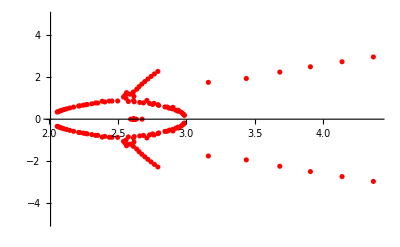

```mathematica
ListPlot[Map[{Re[#[[2]]],Im[#[[2]]]}&,Select[Flatten[Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[JacobsThalGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]],PlotStyle->{Transparent[0.5], Red}]
```

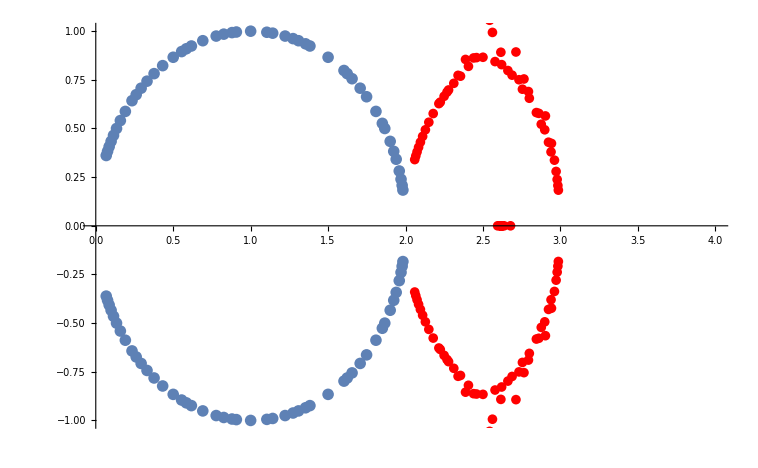

```mathematica
Show[
ListPlot[Map[{Re[#[[2]]],Im[#[[2]]]}&,Select[Flatten[Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]],PlotRange->{{0,4},All}],ListPlot[Map[{Re[#[[2]]],Im[#[[2]]]}&,Select[Flatten[Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[JacobsThalGraph[k],x]],{k,3,18}]]]]}]],Length[#]==2&]],PlotStyle->{Transparent[0.5], Red}]

]
```

```mathematica
Map[{Re[#[[2]]],Im[#[[2]]]}&,Select[Flatten[Table[ExpressionToList[N[Roots[k==0,x]]],{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CompleteGraph[k],x]],{k,3,10}]]]]}]],Length[#]==2&]]//ListPlot
```

-Graphics-

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

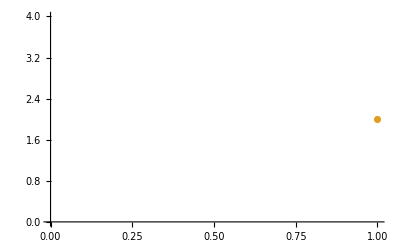
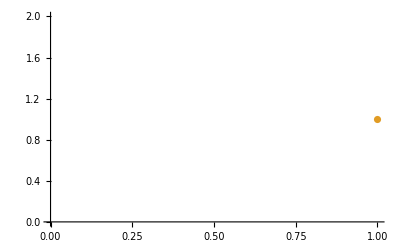
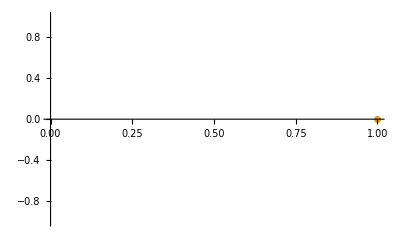
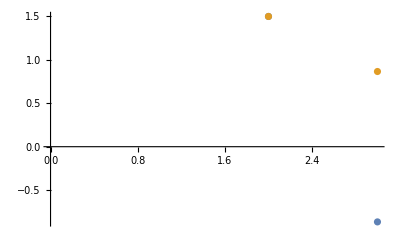
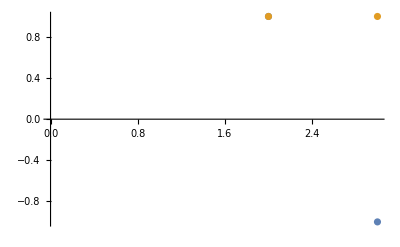
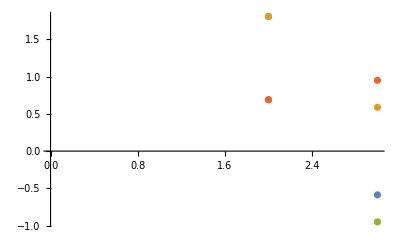
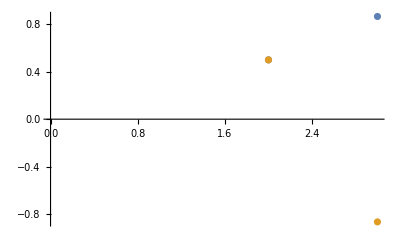
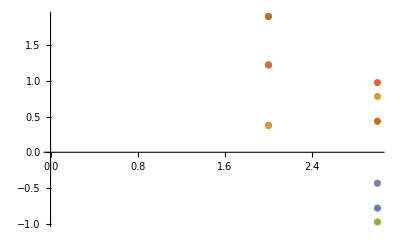

```mathematica
Table[Map[{#,Re[#[[2]]],Im[#[[2]]]}&,ExpressionToList[N[Roots[k==0,x]]]]//ListPlot,{k,Rest[DeleteDuplicates[Flatten[Table[FactorList[ChromaticPolynomial[CycleGraph[k],x]],{k,3,20}]]]]}]
```

```mathematica
Map[{#[[2]]}&,ToRules[N[Roots[19-171 x+969 x^2-3876 x^3+11628 x^4-27132 x^5+50388 x^6-75582 x^7+92378 x^8-92378 x^9+75582 x^10-50388 x^11+27132 x^12-11628 x^13+3876 x^14-969 x^15+171 x^16-19 x^17+x^18==0,x]]]]
```

Map::optx: Unknown option x in Map[{#1⟦2⟧}&,{x→0.0541828-0.324699 ⅈ},{x→0.0541828+0.324699 ⅈ},{x→0.210859-0.614213 ⅈ},{x→0.210859+0.614213 ⅈ},{x→0.453052-0.837166 ⅈ},{x→0.453052+0.837166 ⅈ},{x→0.754515-0.9694 ⅈ},{x→0.754515+0.9694 ⅈ},{x→1.08258-0.996584 ⅈ},«9»].

Map[{#1⟦2⟧}&,{x→0.0541828-0.324699 ⅈ},{x→0.0541828+0.324699 ⅈ},{x→0.210859-0.614213 ⅈ},{x→0.210859+0.614213 ⅈ},{x→0.453052-0.837166 ⅈ},{x→0.453052+0.837166 ⅈ},{x→0.754515-0.9694 ⅈ},{x→0.754515+0.9694 ⅈ},{x→1.08258-0.996584 ⅈ},{x→1.08258+0.996584 ⅈ},{x→1.4017-0.915773 ⅈ},{x→1.4017+0.915773 ⅈ},{x→1.67728-0.735724 ⅈ},{x→1.67728+0.735724 ⅈ},{x→1.87947-0.475947 ⅈ},{x→1.87947+0.475947 ⅈ},{x→1.98636-0.164595 ⅈ},{x→1.98636+0.164595 ⅈ}]

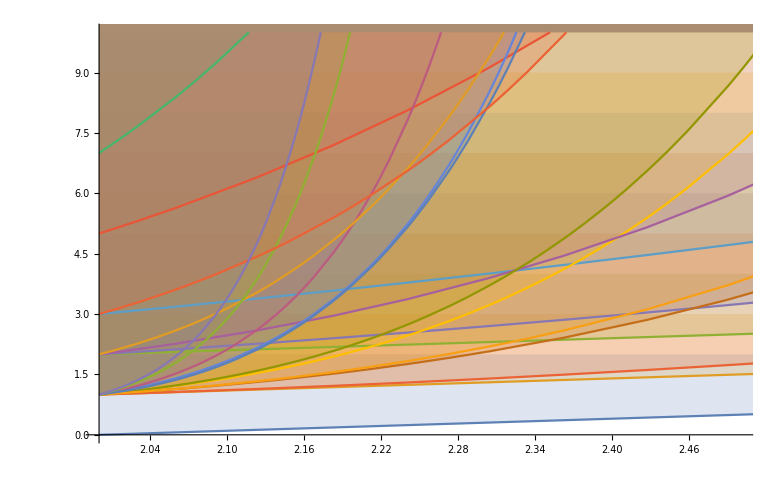

```mathematica
Plot[{-2+x,-1+x,x,3-3 x+x^2,2-2 x+x^2,5-10 x+10 x^2-5 x^3+x^4,1-x+x^2,7-21 x+35 x^2-35 x^3+21 x^4-7 x^5+x^6,2-4 x+6 x^2-4 x^3+x^4,3-9 x+18 x^2-21 x^3+15 x^4-6 x^5+x^6,1-2 x+4 x^2-3 x^3+x^4,11-55 x+165 x^2-330 x^3+462 x^4-462 x^5+330 x^6-165 x^7+55 x^8-11 x^9+x^10,1-2 x+5 x^2-4 x^3+x^4,13-78 x+286 x^2-715 x^3+1287 x^4-1716 x^5+1716 x^6-1287 x^7+715 x^8-286 x^9+78 x^10-13 x^11+x^12,1-3 x+9 x^2-13 x^3+11 x^4-5 x^5+x^6,1-4 x+14 x^2-28 x^3+39 x^4-36 x^5+21 x^6-7 x^7+x^8,2-8 x+28 x^2-56 x^3+70 x^4-56 x^5+28 x^6-8 x^7+x^8,17-136 x+680 x^2-2380 x^3+6188 x^4-12376 x^5+19448 x^6-24310 x^7+24310 x^8-19448 x^9+12376 x^10-6188 x^11+2380 x^12-680 x^13+136 x^14-17 x^15+x^16,1-3 x+12 x^2-19 x^3+15 x^4-6 x^5+x^6,19-171 x+969 x^2-3876 x^3+11628 x^4-27132 x^5+50388 x^6-75582 x^7+92378 x^8-92378 x^9+75582 x^10-50388 x^11+27132 x^12-11628 x^13+3876 x^14-969 x^15+171 x^16-19 x^17+x^18},{x,2,5}, PlotRange->{{2,2.5},{0,10}}, Filling->Table[{k->k+1},{k,20}]]
```